```mathematica
PtxZero = 10^-2;
Ptxi =10^-3;
a=4;
rD = 130;
rZero = 60;
rZeroD = 80;
n = 10^-11;
vZeroD=1;
vD=1;
vZero=1;
```

```mathematica
hZeroD=PtxZero/(rZeroD^a);
hD= Ptxi/(rD^a);
hZero = Ptxi/(rZero^a);
beta = (vZeroD*hZeroD)/(vD *hD);
```

```mathematica
gamma =2.5
```

2.5

```mathematica
Pd= Exp[-(gamma *n)/(vD *hD)];
PZero=Exp[-(gamma *n)/(vZero *hZero)];
G=10^(-10)
q=0.1;
qZero = 0.99
nUsers=50;
```

1/10000000000

0.99

```mathematica
PZeroiZero[i_]:=PZero(1/(1+gamma))^(i-1)
```

```mathematica
PZeroiOne[i_]:= PZeroiZero[i](1+gamma* rZero^a* G)^-1
```

```mathematica
PDiZero[i_]:=Pd*(1/(1+gamma))^(i-1)
```

```mathematica
PDiOne[i_]:=PDiZero[i]/(1+(beta *gamma))
```

```mathematica
PZeroD[i_]:=Exp[-(gamma* n)/(vZero* hZero)](1/(1+gamma/beta))^i
```

```mathematica
rZeroF[k_,PrxOn_] :=PrxOn*∑_(i=k)^nUsers Binomial[  nUsers,i]*Binomial[i,k]*q^i *(1-q)^( nUsers-i)*PZeroiZero[i]^k*(1-PDiZero[i])^k*(1-PZeroiZero[i]*(1-PDiZero[i]))^(i-k)
rOneF[k_,PrxOn_, PtxOn_] := PrxOn*((1-qZero*PtxOn)*∑_(i=k)^nUsers Binomial[nUsers,i] *Binomial[i, k]*q^i *(1-q)^(nUsers-i)*PZeroiZero[i]^k*(1-PDiZero[i])^k*(1-PZeroiZero[i]*(1-PDiZero[i]))^(i-k)+ qZero*PtxOn*∑_(i=k)^nUsers Binomial[nUsers,i]*Binomial[i, k]*q^i *(1-q)^(nUsers-i)*PZeroiOne[i]^k*(1-PDiOne[i])^k*(1-PZeroiOne[i]*(1-PDiOne[i]))^(i-k))
```

```mathematica
pQueueDecreasedByOne[ PtxOn_] :=  qZero*PtxOn*∑_(k=0)^nUsers Binomial[nUsers,k] q^k *(1-q)^(nUsers-k)PZeroD[k]*(1-PZeroiOne[k](1-PDiOne[k]))^k
```

```mathematica
pQueueInreasedByOne[k_,PrxOn_, PtxOn_] :=PrxOn*((1-qZero*PtxOn)∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)PZeroiZero[i]^k (1-PDiZero[i])^k(1-PZeroiZero[i](1-PDiZero[i]))^(i-k)+qZero*PtxOn*∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)(1- PZeroD[i])PZeroiOne[i]^k(1-PDiOne[i])^k(1-PZeroiOne[i](1-PDiOne[i]))^(i-k)+qZero*PtxOn*∑_(i=k+1)^nUsers Binomial[nUsers,i] Binomial[i, k+1] q^i*(1-q)^(nUsers-i) PZeroD[i] PZeroiOne[i]^(k+1)(1-PDiOne[i])^(k+1)(1-PZeroiOne[i](1-PDiOne[i]))^(i-k-1))
```

```mathematica
pQueueInreasedByOneWhenZero[PrxOn_, PtxOn_] := 1-pQueueDecreasedByOne[ PtxOn]-∑_(i=1)^nUsers pQueueInreasedByOne[i,PrxOn, PtxOn]
```

```mathematica
pQueueInreasedByZero[k_, PrxOn_]:=PrxOn*∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)PZeroiZero[i]^k *(1-PDiZero[i])^k*(1-PZeroiZero[i](1-PDiZero[i]))^(i-k)
```

```mathematica
lambdaZero[PrxOn_]:=∑_(k=1)^nUsers k  *rZeroF[k,PrxOn]
```

```mathematica
lambdaOne[PrxOn_, PtxOn_]:=∑_(k=1)^nUsers k* rOneF[k,PrxOn, PtxOn]
```

```mathematica
probQueueIsEmpty [PrxOn_, PtxOn_] :=(pQueueDecreasedByOne[ PtxOn] -∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] )/(pQueueDecreasedByOne[ PtxOn]-(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn])+lambdaZero [PrxOn])
probQueueIsEmpty [1, 0.5]
```

0.682103

```mathematica
avgQueueLength [PrxOn_, PtxOn_] :=1/(2(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] -pQueueDecreasedByOne[PtxOn] )(pQueueDecreasedByOne[PtxOn]-(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn])+lambdaZero [PrxOn]))((∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] -pQueueDecreasedByOne[PtxOn] )(∑_(i=1)^nUsers i *(i+3)*pQueueInreasedByZero[i, PrxOn])+lambdaZero[PrxOn](2pQueueDecreasedByOne[ PtxOn]-∑_(i=1)^nUsers i *(i+3)*pQueueInreasedByOne[i,PrxOn, PtxOn]))
```

```mathematica
ThroughputDirect [PrxOn_,PtxOn_]:= (qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn])* ∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)*PDiOne[k+1])+((1-qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]))*∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)*PDiZero[k+1])
```

```mathematica
ThroughputRelay[PrxOn_, PtxOn_] := PrxOn*((qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]) *(∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)* (1-PDiOne[k+1])*PZeroiOne[k+1]))+( (1-qZero* PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn])) *(∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k) *(1-PDiZero[k+1])*PZeroiZero[k+1])))
```

```mathematica
serviceRate[PtxOn_]:= PtxOn*∑_(k=0)^nUsers Binomial[nUsers,k]*qZero *q^k*(1-q)^(nUsers-k)*PZeroD[k]
```

```mathematica
(*Plot[serviceRate[p],{p,0,1}]*)
```

```mathematica
arrivalRate[PrxOn_, PtxOn_]:=  (lambdaZero[PrxOn] *PtxOn*probQueueIsEmpty[PrxOn, PtxOn] + PrxOn*(1-PtxOn ))+(lambdaOne[PrxOn, PtxOn]* PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]))

arrivalRateNEW[PrxOn_, PtxOn_]:=  (lambdaZero[PrxOn] *probQueueIsEmpty[PrxOn, PtxOn] )+ (lambdaOne[PrxOn, PtxOn]* (1-probQueueIsEmpty[PrxOn, PtxOn]))
```

```mathematica
(*Plot3D[arrivalRate[Rx,Tx],{Rx,0,1},{Tx,0,1},AxesLabel->Automatic]*)
```

```mathematica
(*Plot3D[arrivalRateNEW[Rx,Tx],{Rx,0,1},{Tx,0,1},AxesLabel->Automatic]*)
```

```mathematica
nUsers
```

50

```mathematica
(*NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]≥ arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}]*)
```

```mathematica
(*gamma*)
```

```mathematica
TableForm[ results= Table[
{nUsers,Values[ NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]> arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[2]] ][[1]],
Values[ NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]> arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[2]] ][[2]],

NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]> arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[1]]
}, 
{nUsers,50} ] ];
```

```mathematica
TableForm[results,TableHeadings->{None,{"# Users","P(Tx=on)","P(Rx=on)","throughput/user"}}]
```

# Users | P(Tx=on) | P(Rx=on) | throughput/user
1 | 0.993775 | 1. | 0.0723214
2 | 0.993775 | 1. | 0.067136
3 | 0.993775 | 1. | 0.0623249
4 | 0.993775 | 1. | 0.0578607
5 | 0.993775 | 1. | 0.0537181
6 | 0.993775 | 1. | 0.0498735
7 | 0.993775 | 1. | 0.0463054
8 | 0.993775 | 1. | 0.0429935
9 | 0.993775 | 1. | 0.0399194
10 | 0.993775 | 1. | 0.0370658
11 | 0.993775 | 1. | 0.0344168
12 | 0.993775 | 1. | 0.0319576
13 | 0.993775 | 1. | 0.0296746
14 | 0.993775 | 1. | 0.0275549
15 | 0.993775 | 1. | 0.0255869
16 | 0.993775 | 1. | 0.0237597
17 | 0.993775 | 1. | 0.0220632
18 | 0.993775 | 1. | 0.0204879
19 | 0.993775 | 1. | 0.0190253
20 | 0.993775 | 1. | 0.0176671
21 | 0.993775 | 1. | 0.016406
22 | 0.993775 | 1. | 0.0152349
23 | 0.993775 | 1. | 0.0141475
24 | 0.993775 | 1. | 0.0131377
25 | 0.993775 | 1. | 0.0122
26 | 0.993775 | 1. | 0.0113293
27 | 0.993775 | 1. | 0.0105207
28 | 0.993775 | 1. | 0.0097698
29 | 0.993775 | 1. | 0.00907253
30 | 0.993775 | 1. | 0.00842501
31 | 0.993775 | 1. | 0.00782371
32 | 0.993775 | 1. | 0.00726532
33 | 0.993775 | 1. | 0.00674678
34 | 0.993775 | 1. | 0.00626524
35 | 0.993775 | 1. | 0.00581807
36 | 0.993775 | 1. | 0.0054028
37 | 0.993775 | 1. | 0.00501717
38 | 0.993775 | 1. | 0.00465906
39 | 0.993775 | 1. | 0.00432651
40 | 0.993775 | 1. | 0.00401768
41 | 0.99348 | 1. | 0.00373089
42 | 0.99348 | 1. | 0.00346457
43 | 0.99348 | 1. | 0.00321726
44 | 0.99348 | 1. | 0.0029876
45 | 0.99348 | 1. | 0.00277432
46 | 0.99348 | 1. | 0.00257627
47 | 0.99348 | 1. | 0.00239235
48 | 0.99348 | 1. | 0.00222156
49 | 0.99348 | 1. | 0.00206296
50 | 0.99348 | 1. | 0.00191568

```mathematica
(*ListPointPlot3D[Table[ThroughputDirect[Rx,Tx],{Rx,0.01,1.0,0.01},{Tx,0.01,1.0,0.01}]]*)
```

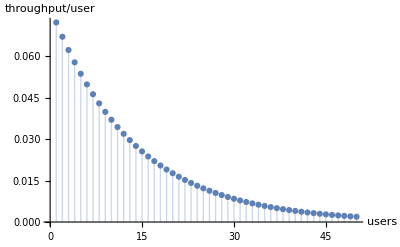

```mathematica
usersIdx=Table[results[[i,1]],{i,1,50}];
TxON = Table[results[[i,2]],{i,1,50}];RxON = Table[results[[i,3]],{i,1,50}];
perUserThroughput=Table[results[[i,4]],{i,1,50}];
ListPlot[Table[{usersIdx[[i]],perUserThroughput[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, throughput/user}]

(*avgQueueLength[TxON,RxON]*)
```

```mathematica
(*ListPlot[avgQueueLength[TxON,RxON],Filling->Axis, AxesLabel->{ users, "avg. queue size"}]*)
G
gamma
```

1/10000000000

2.5

```mathematica
perUserThroughput
```

{0.0723214,0.067136,0.0623249,0.0578607,0.0537181,0.0498735,0.0463054,0.0429935,0.0399194,0.0370658,0.0344168,0.0319576,0.0296746,0.0275549,0.0255869,0.0237597,0.0220632,0.0204879,0.0190253,0.0176671,0.016406,0.0152349,0.0141475,0.0131377,0.0122,0.0113293,0.0105207,0.0097698,0.00907253,0.00842501,0.00782371,0.00726532,0.00674678,0.00626524,0.00581807,0.0054028,0.00501717,0.00465906,0.00432651,0.00401768,0.00373089,0.00346457,0.00321726,0.0029876,0.00277432,0.00257627,0.00239235,0.00222156,0.00206296,0.00191568}

```mathematica
qZero
```

0.99

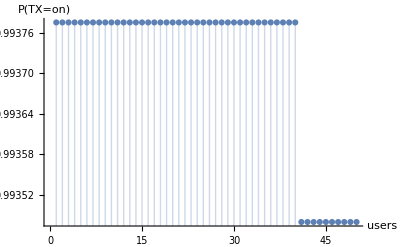

```mathematica
ListPlot[Table[{usersIdx[[i]],TxON[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, "P(TX=on)"}]
```

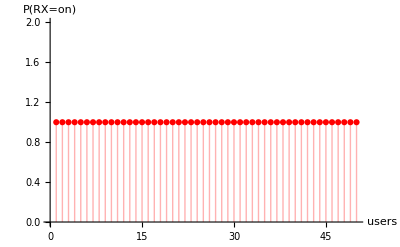

```mathematica
ListPlot[Table[{usersIdx[[i]],RxON[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, "P(RX=on)"},PlotStyle->{Red,Thick}]
```

```mathematica
gamma
```

2.5

```mathematica
G
```

1/10000000000

```mathematica
TxON
```

{0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.99348,0.99348,0.99348,0.99348,0.99348,0.99348,0.99348,0.99348,0.99348,0.99348}

```mathematica
RxON
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}